Your Title Here

```mathematica
R=8.314;Pc=22.12;Tc=647.3;κ=0.8732;
```

```mathematica
A[T_,P_]:=0.4572355289*(1+κ*(1-√(T/Tc)))^2*(Tc/T)^2*P/Pc;
```

```mathematica
B[T_,P_]:=0.0777960739*Tc/T*P/Pc;
```

```mathematica
Z[T_,P_]:=Module[{a2,a1,a0,p,q,r,x,zlist},
a2=B[T,P]-1;
a1=A[T,P]-3*B[T,P]^2-2*B[T,P];
a0=-(A[T,P]*B[T,P]-B[T,P]^2-B[T,P]^3);
p=(3*a1-a2^2)/3;
q=(2*a2^3-9*a2*a1+27*a0)/27;
r=q^2/4+p^3/27;
x=If[r>0,{CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]},Module[{m,θ},m=2*√(-p/3);θ=ArcCos[(3*q)/(p*m)]/3;{m*Cos[θ],m*Cos[θ+4*π/3],m*Cos[θ+2*π/3]}]];
zlist=x-a2/3;
DeleteDuplicates@{First@zlist(*V*),Last@zlist(*L*)}];
```

```mathematica
V[T_,P_]:=Z[T,P]*R*T/P;
```

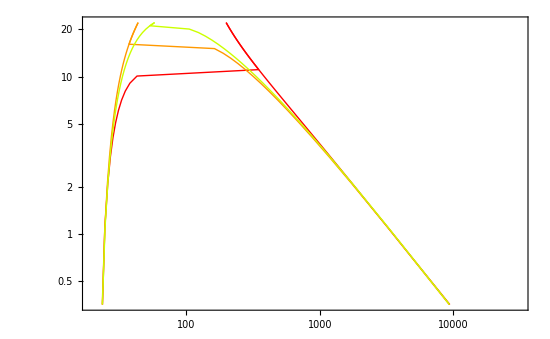

```mathematica
Module[{a,b,c,Tsat},
a={3.55959,5.40221,5.20389};
b={643.748,1838.675,1733.926};
c={-198.043,-31.737,-39.485};

Tsat[P_,n_]:=t/.Quiet@Solve[10*P==10^(a-b/(t+c))[[n]],t][[1]];

(*ListLogLogPlot[Table[{First@V[Tsat[#,i],#],#}&/@Range[0.1,Pc],{i,1,Length@a}],Joined->True,PlotStyle->({Thick,Hue[#]}&/@Range[0,0.9,0.1]),
Frame->True,ImageSize->550]*)
ListLogLogPlot[Table[{
{First@V[Tsat[#,i],#],#}&/@Range[0.1,Pc],
{Last@V[Tsat[#,i],#],#}&/@Range[0.1,Pc]
},{i,1,Length@a}],Joined->True,PlotStyle->({Thick,Hue[#]}&/@Range[0,0.9,0.1]),
Frame->True,ImageSize->550];

Table[{
{First@V[Tsat[#,i],#],#}&/@Range[0.1,Pc],
{Last@V[Tsat[#,i],#],#}&/@Range[0.1,Pc]
},{i,1,Length@a}];

ListLogLogPlot[{
{First@V[Tsat[#,2],#],#}&/@Range[0.1,Pc],
{Last@V[Tsat[#,2],#],#}&/@Range[0.1,Pc]
},Joined->True,PlotStyle->({Thick,Hue[#]}&/@Range[0,0.9,0.1]),
Frame->True,ImageSize->550];

ListLogLogPlot[Table[{
{{First@V[Tsat[#,i],#],#}}&/@Range[0.1,Pc],
{{Last@V[Tsat[#,i],#],#}}&/@Range[0.1,Pc]
},{i,1,Length@a}],Joined->True,(*PlotStyle->({Thick,Hue[#]}&/@Range[0,0.9,0.1]),*)
Frame->True,ImageSize->550];

Show[
Table[
ListLogLogPlot[{
{First@V[Tsat[#,i],#],#}&/@Range[0.1,Pc],
{Last@V[Tsat[#,i],#],#}&/@Range[0.1,Pc]
},Joined->True,PlotStyle->{{Thick,{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9]}[[i]]}}],
{i,1,Length@a}],
Frame->True,ImageSize->550]
]
```

```mathematica
Hue@#&/@Range[0,0.9,0.1]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9]}





```mathematica
(*Show[
ListLogLogPlot[{Last@V[Tsat@#,#],#}&/@Range[0.1,Pc],Joined->True,PlotStyle->{Thick,Black}],
ListLogLogPlot[Table[{First@V[Tsat[#,i],#],#}&/@Range[0.1,Pc],{i,1,Length@a}],Joined->True,PlotStyle->({Thick,Hue[#]}&/@Range[0,0.9,0.1])],
Frame->True,ImageSize->550]*)
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX